# MATH299M/CMSC389W - Visualization through Mathematica Week 7: Graphics: Graphics, Points, Lines, Shapes, Graphics3D, GraphicsGrid, Show

Graphics

Read for Graphics?? Graphics allows for quick drawing of shapes in a blank space. It takes one argument, which is a list of Graphics Primitives, that is, objects that are made especially to be put into Graphics, each with its own set of rules, and it draws them all in the same space. After that argument you can add Options.

Point
Point takes in a coordinate pair to plot a point. You can also give Point a list of coordinate pairs to plot multiple points. It will automatically fit the frame and center everything, but we can use the PlotRange option.

```mathematica
Graphics[Point[{1,1}]]
```

-Graphics-

```mathematica
Graphics[{Point[{{0,0},{0,1},{1,0}}]},PlotRange->2]
```

-Graphics-

Line
Line takes in a list of coordinate pairs and connect the dots.

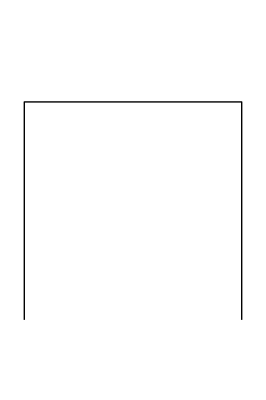

```mathematica
Graphics[Line[{{0,0},{0,1},{1,1},{1,0}}],PlotRange->{-.2,1.3}]
```

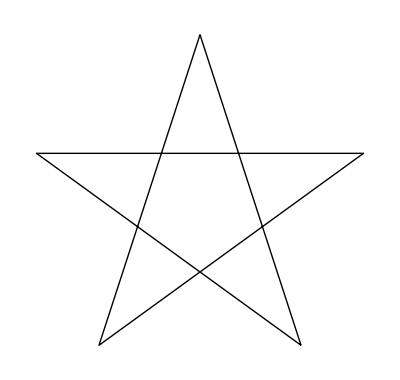

```mathematica
Graphics[Line[{{1,0},{1+2Cos[72/360 2π]-2Cos[36/360 2π],2Sin[108/360 2π]+2Sin[36/360 2π]},{-1,0},{1+2Cos[72/360 2π],2Sin[72/360 2π]},{-1-2Cos[72/360 2π],2Sin[72/360 2π]},{1,0}}]]
```

But now if you wanted to make a star without having to do all that math there is a much nicer way to accomplish that.

```mathematica
v=Table[15 {Cos[t],Sin[t]},{t,0,4 Pi,4 Pi/5}];
```

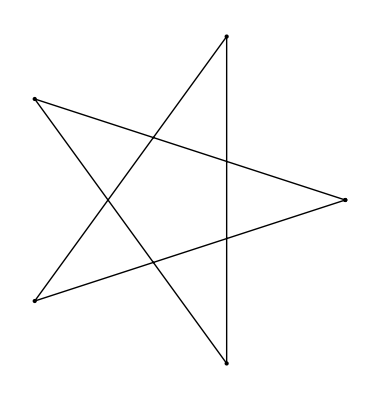

```mathematica
Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Line[{1,2,3,4,5,6}]}]]
```

If for some reason you feel a need to give the expression of your graphics object feel free to do so by using Inset. This is very nice if dealing with very heavy expressions.

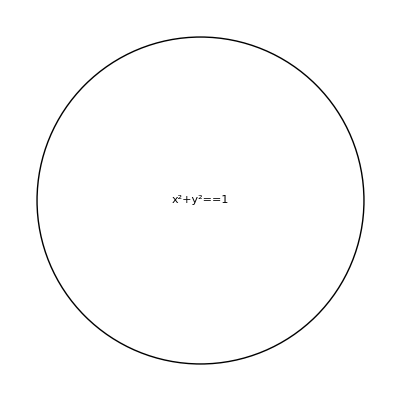

```mathematica
Graphics[{Circle[],Inset[x^2+y^2==1,{0,0}]}]
```

Tick Marks
Now if you want to draw something and indicate spots along the x and y axis you have tick marks available to you

Place them automatically

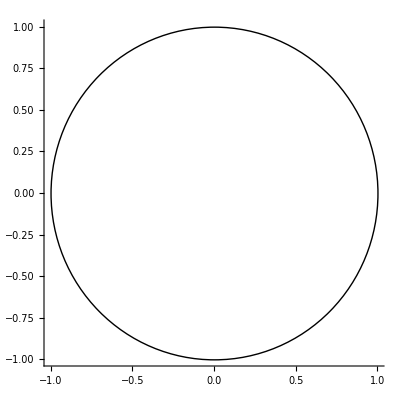

```mathematica
Graphics[Circle[],Axes->True,Ticks->Automatic]
```

Or specify your tick marks to a location.

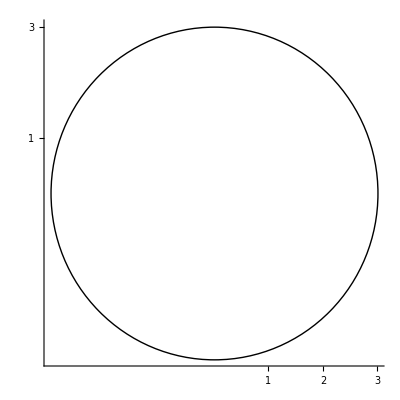

```mathematica
Graphics[Circle[{0,0},3],Ticks->{{1,2,3},{1,3}},Axes->True]
```

Now if for some reason you wanted colors because black and white does not satisfy you enough

```mathematica
Graphics[Circle[],Axes->True,TicksStyle->{Directive[Red,Bold],Directive[Blue,12]}]
```

-Graphics-

Color defined in-line
If you want to change colors, just type the color, and everything after it in the list will be that color, default is black. You can also specify a color as usual with RGBColor[r,g,b].

```mathematica
Graphics[{Red,Point[{0,0}],RGBColor[0,0,1],Point[{1,1}]},PlotRange->2]
```

-Graphics-

Circle, Disk, Rectangle, Polygon
Circle and Disk: Center as coordinate pair, then radius
Rectangle: Coordinates of bottom left corner and top right corner
Polygon: List of points, draws a filled in polygon, automatically connects first and last point, can be concave
Text: String and coordinate to be centered at

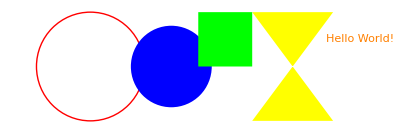

```mathematica
Graphics[{Red,Circle[{0,0},1],Blue,Disk[{1.5,0},.75],Green,Rectangle[{2,0},{3,1}],Yellow,Polygon[{{3,-1},{4.5,1},{3,1},{4.5,-1}}],Orange,Text["Hello World!",{5,.5}]}]
```

Object Options
Opacity, thickness, dashed, point size, Style for text: size, font, typeface.

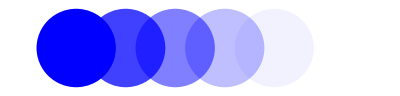

```mathematica
Graphics[{Blue,Opacity[1],Disk[{0,0},1],Opacity[.75],Disk[{1.25,0},1],Opacity[.5],Disk[{2.5,0},1],Opacity[.25],Disk[{3.75,0},1],Opacity[.05],Disk[{5,0},1],Opacity[0],Disk[{6.25,0},1]}]
```

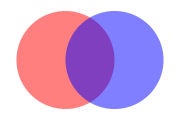

```mathematica
Graphics[{Opacity[.5],Red,Disk[{0,0},1],Blue,Disk[{1,0},1]},ImageSize->Small]
```

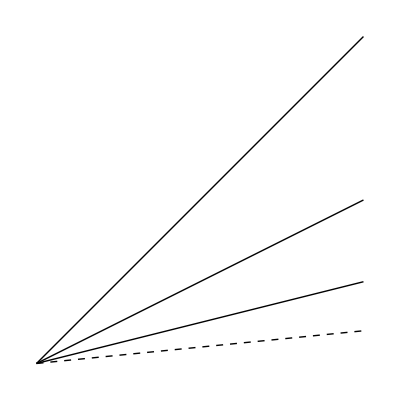

```mathematica
Graphics[{Line[{{0,0},{1,1}}],Thin,Line[{{0,0},{1,.5}}],Thick,Line[{{0,0},{1,.25}}],Dashed,Line[{{0,0},{1,.1}}]}]
```

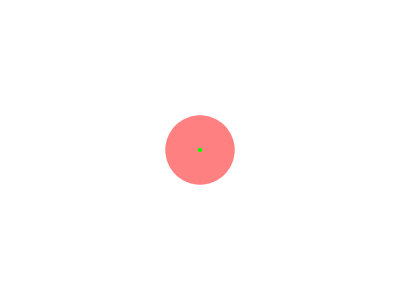

```mathematica
Graphics[{PointSize[1],Pink,Point[{0,0}],PointSize[Large],Orange,Point[{0,0}],PointSize[Medium],Yellow,Point[{0,0}],PointSize[Small],Green,Point[{0,0}],PlotRange->10}]
```

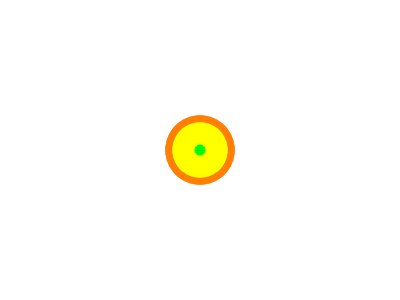

```mathematica
Graphics[{PointSize[1],Pink,Point[{0,0}],PointSize[.5],Orange,Point[{0,0}],PointSize[.1],Yellow,Point[{0,0}],PointSize[.02],Green,Point[{0,0}],PointSize[.001],Blue,Point[{0,0}],PlotRange->10}]
```

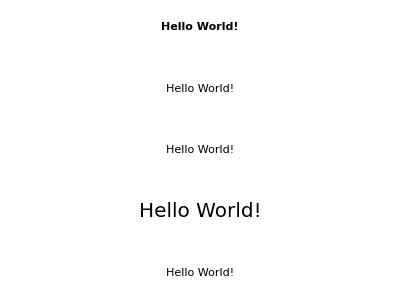

```mathematica
Graphics[{Text[Style["Hello World!",Bold],{0,0}],Text[Style["Hello World!",Italic],{0,-.25}],Text[Style["Hello World!",Underlined],{0,-.5}],Text[Style["Hello World!",FontSize->20],{0,-.75}],Text[Style["Hello World!",FontFamily->"Monotype Corsiva"],{0,-1}]}]
```

Graphics3D

Graphics3D is very similar; in general everything will need 3 coordinates now. We also have different Primitives, such as the Sphere.
Sphere: Center coordinate triplet, radius
Cylinder: Two coordinate triplets to determine center line, radius
Cuboid: Two coordinate triplets for bottom left front and top right back corners

```mathematica
Graphics3D[{Magenta,Sphere[{0,0,0},1],Cyan,Cylinder[{{-1,0,-1},{-2,0,1}},.3],Gray,InfinitePlane[{{0,0,-1.5},{1,1,-1.5},{2,3,-1.5}}],Blue,Cuboid[{1.25,0,-1},{2.75,2,1}]},PlotRange->3,ImageSize->Medium]
```

-Graphics3D-

A lot of uses of graphics 3D come when dealing with 3D images:

Most of Mathematica’s data sources require the use of 3D images, like if you wanted to see your favorite molecule!

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

-Graphics3D-

You can even see specific geometric representations of animals...

```mathematica
ExampleData[{"Geometry3D","Cow"}]
```

-Graphics3D-

And when you get to importing and exporting, the use of 3D becomes very important

```mathematica
Import["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=1tf6","PDB",Background->GrayLevel[0.1],ImageSize->Medium]
```

-Graphics3D-

You can even mess with the lighting that exists on any specific 3D object. We would be impressed if someone could create optical allusions with this:

```mathematica
Graphics3D[{Lighting->{{"Point",Red,{0,0,2}}},Sphere[],Lighting->{{"Spot",Yellow,{{3,0,2},{3,0,0}},Pi/8}},Sphere[{3,0,0}],Lighting->{{"Directional",Blue,{{0,3,2},{0,3,0}}}},Sphere[{0,3,0}],Lighting->{{"Point",White,{3,3,2}}},Sphere[{3,3,0}]}]
```

-Graphics3D-

GraphicsGrid

GraphicsGrid takes in an array of things, a list of lists, and displays them in a grid. It’s a good tool for showing many Plots and Graphics at once that you want to compare.

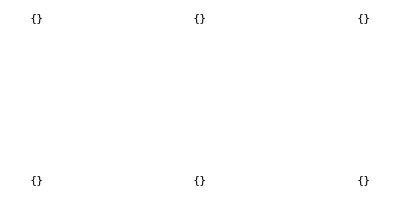

```mathematica
GraphicsGrid[{Table[{Graphics[{color,Disk[{0,0},1]},ImageSize->800,PlotRange->8]},{color,{Red,Pink,Blue}}],Table[{Graphics[{color,Rectangle[{-1,-1},{1,1}]},ImageSize->800,PlotRange->8]},{color,{Orange,Yellow,Green}}]}]
```

Show

Show will superimpose all of its arguments, given that they’re the same dimension. That is, you can’t superimpose a Graphics3D object with a Plot object.

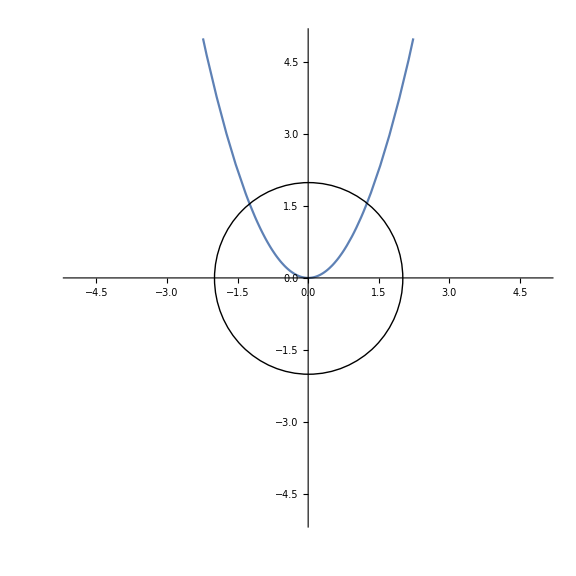

```mathematica
Show[Plot[x^2,{x,-5,5},PlotRange->5,AspectRatio->1,ImageSize->Large],Graphics[Circle[{0,0},2]]]
```

You can get a whole lot more cool when you add things on top of your graphics:

You can create an entire analog clock that is the exact time of day using graphics.

Let' s decompose what is going on here. First we have all of the code nested inside Dynamic, this allows the clock hands to move as appropriate. Then we give it the initial time spots and assign each to the respective hour, mind, sec etc...
Our graphics object than has the primitives arrowhead, arrow, line and PointSize. The table is used for the creation of the dots that represent hour marking.

```mathematica
Dynamic@Module[{hour,min,sec,ht,mt,st},Clock[];{hour,min,sec}=Take[DateList[],-3];
ht=Pi/2-2 Pi hour/12-2 Pi min/720;mt=Pi/2-2 Pi min/60;
st=Pi/2-2 Pi Floor[sec]/60;
Graphics[{Arrowheads[0.1],Arrow[{{0,0},0.6 {Cos[ht],Sin[ht]}}],Arrow[{{0,0},0.85 {Cos[mt],Sin[mt]}}],Line[{{0,0},0.85 {Cos[st],Sin[st]}}],PointSize[Medium],Table[Point[0.9 {Cos[i],Sin[i]}],{i,0,2 Pi,Pi/6}],Point[{0,0}],Circle[]}]]
```

## Ajeet Gary - University of Maryland Experimental Geometry Lab MATH299M/CMSC389W Fall 2018 September 29th, 2018

## Vlad Dobrin - University of Maryland Computer Science MATH299M/CMSC389W Spring 2020 May 29th, 2020